```mathematica
alldata=Import[FileNameJoin[{NotebookDirectory[],"fixtures","output.csv"}]];
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],PlotRange->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[l_List]:=Show[ListLinePlot[Map[Max,l],PlotStyle->Red],ListLinePlot[Map[Min,l],PlotStyle->Blue],ListLinePlot[Map[Mean,l],PlotStyle->Green],PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[dataset,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 x^2-16.7501 x^3+0.329474 x^4]

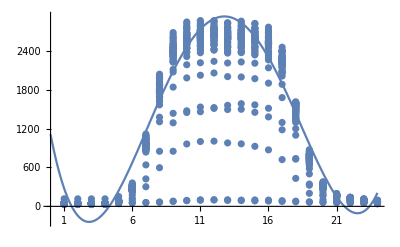

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2015],Monday]],nlm]
```

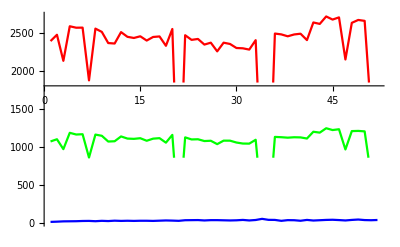

```mathematica
minMaxMeanPlot[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2014],Monday]]]
```

```mathematica
(*Extract all data in mondays which max numbers of parking cars is greater than 2000*)
```

```mathematica
selectedMondays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[dataset,Monday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdata={DateValue[#1,"Hour"]}->#2&@@@Select[alldata,MemberQ[selectedMondays,DateObject[DateList[First[#]][[1;;3]]]]&]
```

{{0}→22,{1}→17,{2}→16,{4}→39,{5}→186,{6}→749,{3}→15,{7}→1529,{8}→2160,{9}→2316,{10}→2363,{11}→2394,{12}→2363,{13}→2359,{14}→2349,{15}→2278,{16}→2094,{17}→1353,{18}→613,{19}→231,{20}→117,{21}→88,{22}→68,{23}→46,{0}→23,2278,{23}→50,{0}→29,{1}→28,{2}→26,{3}→26,{4}→57,{5}→245,{6}→906,{7}→1728,{8}→2389,{9}→2578,{10}→2617,{11}→2633,{12}→2612,{13}→2611,{14}→2595,{15}→2539,{16}→2320,{17}→1583,{18}→764,{19}→287,{20}→147,{21}→96,{22}→69,{23}→48}
 |  |  |  |

```mathematica
p=Predict[trainingdata]
```

PredictorFunction[…]

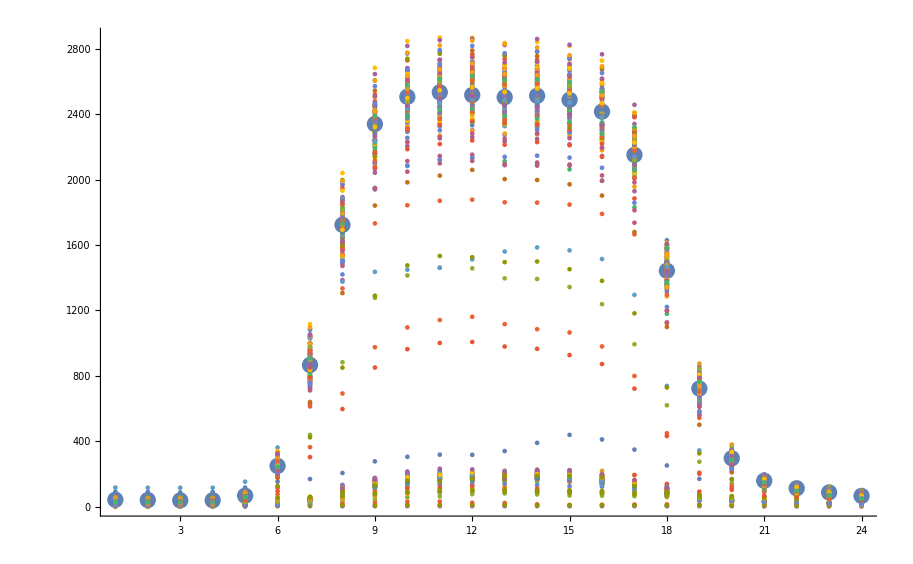

```mathematica
Show[ListPlot[Map[p,Range[0,23]]],ListPlot[Map[Rest,extractDataByWeekday[dataset,Monday]]],PlotRange->All]
```

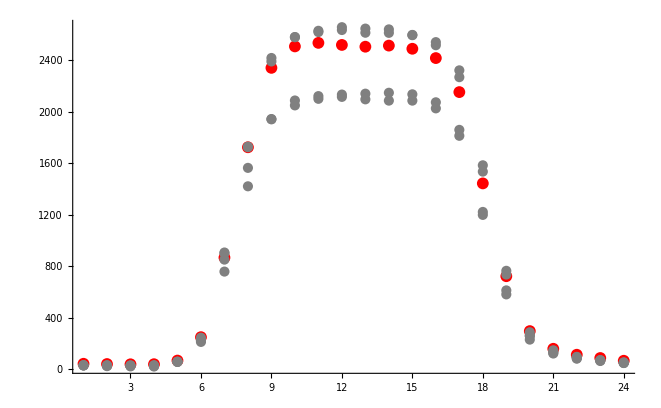

```mathematica
Show[ListPlot[Map[p,Range[0,23]],PlotStyle->Red],ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Monday]],PlotStyle->Gray],PlotRange->All]
```